# Differential operators and simple applications

```mathematica
ClearAll["Global`*"]
```

## 0. Mathematica Basics

## Defining functions

Here is the syntax to define a polynomial and its first derivative:

```mathematica
f[x_]:= x^3+3*x
f'[x_] := D[f[x],x]
```

SetDelayed::write: Tag Function in (3+3 #1^2&)[x_] is Protected.

$Failed

```mathematica
(*exercise: define g as the polynomial x^5 + 5*x + 5, and its derivative g’*)
```

## Displaying outputs and plotting

You can view a defined function as a function of a given variable or evaluate a function at given point(s):

```mathematica
(*view f as a function of x*)
f[x]
(*similarly for f'*)
f'[x]
(*evaluate f at 2*)
f[2]
(*at a sequence of specified points*)
points = {0,1,2,3,4,5,6};
Map[f, points]
```

3 x+x^3

3+3 x^2

14

{0,4,14,36,76,140,234}

```mathematica
(*exercise: evaluate g as a function of y, evaluate it at y=5, and at y = 0,5,100*)
```

```mathematica
(*exercise: evaluate g at 100 evenly spaced points between 0 and 3000*)
```

Now here is how to plot  functions on a given interval:

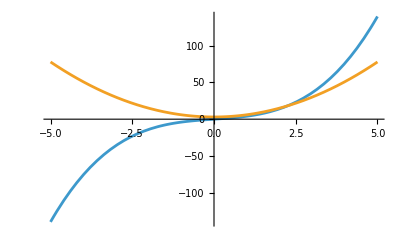

```mathematica
Plot[{f[x], f'[x]},{x, -5,5}]
```

```mathematica
(*exercise: plot g and g' on the interval [-10, 10]*)
```

## 1. Basic linear algebra

## Defining matrices

There are many ways to define matrices, including: nested lists, Array, and Table. There is also in-built code for identity matrices, zero matrices, and random matrices.

```mathematica
(*nested lists*)
A = {
  {1, 20, 29},
  {4.5, 31, 16},
  {70, 8, 9}
}
(*Array: entries are a function of row and column indices*)
B = Array[(#1 + #2) &, {3, 3}]
(*Table: entries generated from i and j*)
C = Table[i*j, {i, 1, 3}, {j, 1, 3}]
```

{{1,20,29},{4.5,31,16},{70,8,9}}

{{2,3,4},{3,4,5},{4,5,6}}

Set::wrsym: Symbol C is Protected.

{{1,2,3},{2,4,6},{3,6,9}}

```mathematica
(*exercise: define a matrix corresponding to the round metric on the unit 2-sphere, with the coordinates being variables a and b*)
```

```mathematica
(*exercise: define a matrix where the entry in the i^th row and j^th column is given by i-j*)
```

## Matrix operations

Some basic matrix operations:

```mathematica
A + IdentityMatrix[3]   (* Add matrices *)
A . B                   (* Matrix multiplication *)
Transpose[A]            (* Transpose *)
Det[A]                  (* Determinant *)
Inverse[A]              (* Inverse *)
```

```mathematica
(*exercise: compute the volume element for the metric on the 2-sphere with radius r*)
```

```mathematica
(*exercise: compute the inverse of the metric of the 2-sphere with radius r*)
```

```mathematica
(*exercise: compute the inverse of the metric of the 2-sphere with radius r*)
```

We can also do some symbolic computations, we will first define a vector of symbolic variables:

```mathematica
n = 3;  (* size of vector / matrix *)
xvec = Table[Subscript[x, i], {i, 1, n}]
```

{x_1,x_2,x_3}

Then we can perform operations on this using the given matrices:

```mathematica
A.xvec
```

{x_1+20 x_2+29 x_3,4.5 x_1+31 x_2+16 x_3,70 x_1+8 x_2+9 x_3}

## 2. Differentiation

Here is an example of a function of 3 variables and the syntax to take partial derivatives. (You can look up how to shorten the notation if there are lots of variables, or how to specify dependence of variables on each other!)

```mathematica
h[x_, y_, z_] := x^3*y^3*z^3 + 2*x*y +3z*y+ 1
(*partial derivatives*)
(*partial derivative of h wrt x:*)
D[h[x,y,z],x]

(*partial derivative of h wrt x and z, as a list*)
variables = {x,z}
partial = Table[D[h[x,y,z],var], {var, variables}]

(*third partial derivative of h wrt x*)
D[h[x,y,z], {x,3}]

(*take another derivative wrt a new set of variables*)
variables2 = {y,z}
partial2 = Table[D[partial, var], {var, variables2}]

(*total derivatives*)
(*total derivative of h*)
Dt[h[x,y]]
(*assuming all other variables depend on x*)
Dt[h[x,y],x]
```

2 y+3 x^2 y^3 z^3

{x,z}

{2 y+3 x^2 y^3 z^3,3 y+3 x^3 y^3 z^2}

6 y^3 z^3

{y,z}

{{2+9 x^2 y^2 z^3,3+9 x^3 y^2 z^2},{9 x^2 y^3 z^2,6 x^3 y^3 z}}

2 y Dt[x]+3 x^2 y^3 Dt[x]+2 x Dt[y]+3 x^3 y^2 Dt[y]

2 y+3 x^2 y^3+2 x Dt[y,x]+3 x^3 y^2 Dt[y,x]

```mathematica
(*exercise*)
(* 1. define a function of 3 variables corresponding to the Euclidean distance from the origin of a point (x,y,z)*)
dist[x_, y_, z_]:= 
(* 2. define the set of variables we will need to compute the gradient*)
variables = 
(* 3. compute the gradient using Table*)
mygradient = 
(* 4. compute the Hessian*)
myhessian =
```

```mathematica
(*exercise*)
(*define r(x,y,z), a(x,y,z), b(x,y,z) to be polar coordinates as functions of x,y, and z*)
r[x_, y_, z_] := 
a[x_, y_, z_] := 
b[x_, y_, z_] := 
(*now compute the Jacobian of the coordinate transformation*)
myjacobian =
```

+ Defining a differential operator:

```mathematica
myoperator[x_] := (D[#, {x,2}]-3D[#,x]+2#)
myoperator[x][f[x]]
```

(2 #1)[3 x+x^3]

## 3. Practice: Wave operator on Schwarzschild exterior

```mathematica
(*Define the metric components*)
schw := {}
```

```mathematica
(*Define function to compute the Laplace-Beltrami operator*)
box_schw[t_, r_, a_, b_] :=
```

```mathematica
(*Write down the effective radial potential obtained after separation of variables*)
V_eff[r_, l_] := 
(*Plot the graph on an appropriate range of r for 3 different values of ell*)
```

## 4. Practice: Wave operator on arbitrary spacetime

```mathematica
(*Define the metric components symbolically*)
```

```mathematica
(*Define a function to compute the volume element*)
```

```mathematica
(*Define function to compute the box operator operator in terms of the metric components*)
```

## 5. Using the xTensor package for symbolic tensor computations

```mathematica
xAct 'xTensor'
```